pdf

ⅇ^((ⅈ π)/(2 alp))

ⅇ^(-(ⅈ π)/(2 alp))

2

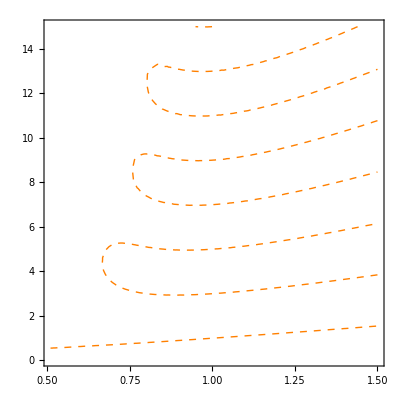

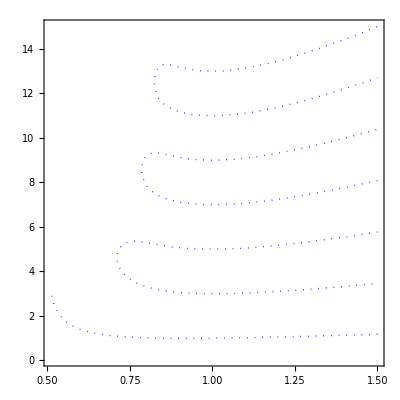

5

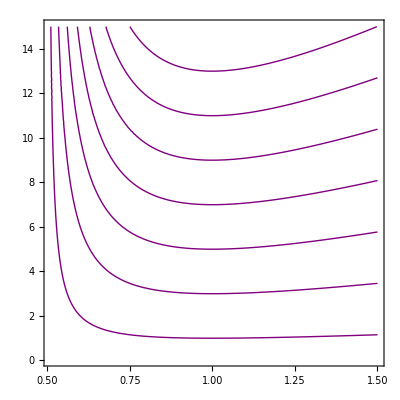

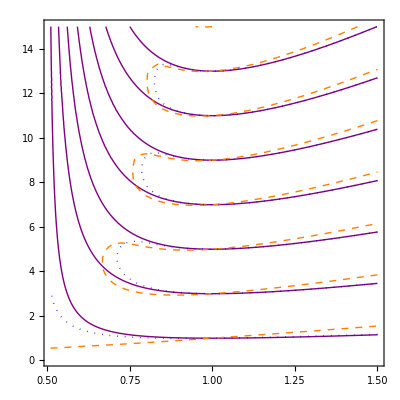

HOZeroesFRC.pdf

```mathematica
Clear[alp]
exportDataType="pdf"

(* Fourier  *)
name = "HOZeroesFou";
fp =  Exp[+I Pi/( 2alp)]
fm =  Exp[-I Pi/( 2alp)]
sinF[x_] = 1/(2 I)(Exp[fp x]- Exp[fm x]);
cosF[x_] = 1/2(Exp[fp x]+ Exp[fm x]);

(* Riemann  *)
name = "HOZeroesRie";
sinR[x_] = x^(2 alp -1)MittagLefflerE[2 alp, 2 alp, -x^(2 alp)];
cosR[x_] = x^(alp-1)MittagLefflerE[2 alp,  alp, -x^(2 alp)];

(* Caputo  *)
name = "HOZeroesCap";
sinC[x_] = x^(a)MittagLefflerE[2 alp, 1+ alp, -x^(2 alp)];
cosC[x_] = MittagLefflerE[2 alp, -x^(2 alp)];

prec = 2
pcR = ContourPlot[cosR[x Pi/2]==0,{alp,0.51,1.5},{x,0.05,15},ContourStyle->{Orange,Dashed,Thick},MaxRecursion->prec]
pcC = ContourPlot[cosC[x Pi/2]==0,{alp,0.51,1.5},{x,0.05,15},ContourStyle->{Blue,Dotted,Thick},MaxRecursion->prec]
prec = 5
pcF = ContourPlot[cosF[x Pi/2]==0,{alp,0.51,1.5},{x,0.05,15},ContourStyle->{Purple,Thick},MaxRecursion->prec]

(*final output*)
fin = Show[{pcF,pcR, pcC}]
name = "HOZeroesFRC";
Export[name<>"."<>exportDataType,fin]
```